```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
threshold = 1;
case=1;
Switch[case,
1,T=100;C0=1;C1=0.4;filename="Fig3a_heatmap.png";
(*2,T=100;C0=1;C1=0.5;filename="Fig3b_heatmap.png";,
3,T=30;C0=1;C1=0.7;filename="Fig3c_heatmap.png";,(*τ2=0.4;τ1=τ2-δ;τ3=1-δ;*)
4,T=30;C0=1;C1=0.5;filename="Fig3d_heatmap.png";*)
]
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=1000;
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

```mathematica
(*Simulation*)
simulation={};
τ2=0.5;τ4=1;
Do[Do[
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.2Min[τ2-τ1,1-τ3]T];
peaks = FindPeaks[Table[V[t],{t,0,maxtime,1}],3,0,threshold];
count=Length[peaks];
point = {τ1,τ3,count/maxtime *1000};
simulation = Append[simulation,point];
,{τ1,0.2,0.499,0.02}],{τ3,0.7,0.999,0.02}];
(*,{τ1,0.1,0.399,0.02}],{τ3,0.6,0.999,0.02}];*)
```

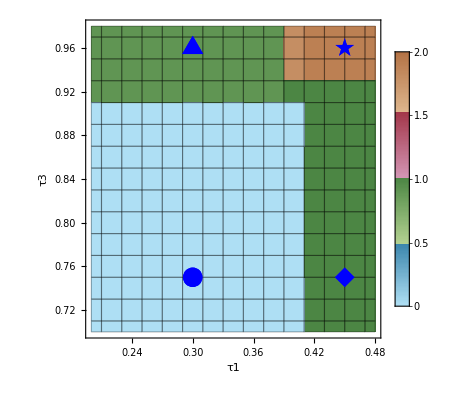

Fig3a_heatmap.png

```mathematica
(*Visualization*)
extract=simulation[[All,{1,2,3}]];
extract=extract.{{1,0,0},{0,1,0},{0,0,T/1000}};
g1= ListDensityPlot[extract,
Mesh->All,
InterpolationOrder->0,
PlotLegends->BarLegend[{Automatic,{0,2}}],
ColorFunction->(ColorData["DarkBands"][0.65*#/2]&),
ColorFunctionScaling->False,
PlotLegends->Automatic,
FrameLabel->{"τ1","τ3"},
PlotRange->{Full,Full,{0,2}},
PlotRangeClipping->False,
LabelStyle->Directive[Black,FontSize->16]
];
g2=ListPlot[{{{0.3,0.75}},{{0.3,0.96}},{{0.45,0.96}},{{0.45,0.75}}},
PlotStyle->PointSize[0.3],
PlotMarkers->{
Style["●",Blue,20],
Style["▲",Blue,25],
Style["★",Blue,20],
Style["◆",Blue,20]
}
];
g3=Show[g1,g2]
Export[filename,g3]
```